```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

```mathematica
Manipulate[
(*Locator array for object & robot(strat & end)*)
o={o1,o2,o3,o4};
r={r1,r2};
(*Create object's(robot, obstacle & border poly)*)
borderpoly =10CirclePoints[x];
robotpoly = Table[Polygon[CirclePoints[n]],{i,2}];
obstaclepoly=Table[Polygon[CirclePoints[i]],{i,4,7,1}];
(*get the minkowski sum between all obstacles & the robot*)
robotobstconfig=Table[findConvexHullCoordsConvexPolysAS[obstaclepoly[[i]],robotpoly[[1]]],{i,1,Length[obstaclepoly],1}];
(* Translate the objects to the respective locator co-ordinates*)
shiftobstaclepoly=
Table[Polygon[Table[obstaclepoly[[j,1,i]]+ o[[j]],{i,1,Length[obstaclepoly[[j,1]]],1}]],{j,1,Length[obstaclepoly],1}];
shiftrobotpoly=Table[Polygon[Table[robotpoly[[j,1,i]]+ r[[j]],{i,1,Length[robotpoly[[j,1]]],1}]],{j,1,Length[robotpoly],1}];
shiftconfigpoints=Table[ Table[robotobstconfig[[j,i]]+o[[j]],{i,1,Length[robotobstconfig[[j]]]}],{j,1,Length[robotobstconfig]}];
(* Create lines from Start & End to all the minkowski region vertices*)
linestoVertices = Table[Table[Table[Line[{r[[k]],shiftconfigpoints[[j,i]]}],{i,1,Length[shiftconfigpoints[[j]]],1}],{j,1,Length[shiftconfigpoints],1}],{k,1,2,1}];
(*Draw all the objects in graphics*)
Graphics[{
EdgeForm[{Thin}]
(*Boundary Polygon*)
,{LightYellow,,Polygon[ borderpoly]}
,{LightGray,linestoVertices }
(*Robot Start*)
,{LightBlue, shiftrobotpoly[[1]]}
(*Robot End*)
,{LightGreen, shiftrobotpoly[[2]]}
(*Obstacles*)
,{LightRed, shiftobstaclepoly}
(*Configuration Space of Robot & Obstacles*)
,{Blue,Line[shiftconfigpoints]}
,{Red,Table[Translate[Point[robotobstconfig[[i]]],o[[i]]],{i,1,Length[robotobstconfig],1}]}
}]
(*Polygon Shape Slider*)
,{n,3,10,1} ,{x,4,9,1} 
(* Intial Robot Locator Position*)
,{{r1,{-4,6}},10{-1,-1},10{1,1},Locator}
,{{r2,{5,-5}},10{-1,-1},10{1,1},Locator}  
,{{o1,{4,5}},10{-1,-1},10{1,1},Locator}
,{{o2,{0,2}},10{-1,-1},10{1,1},Locator}
,{{o3,{-3,-4}},10{-1,-1},10{1,1},Locator}
,{{o4,{3,-3}},10{-1,-1},10{1,1},Locator}
,ContentSize->{380,380}
]
```

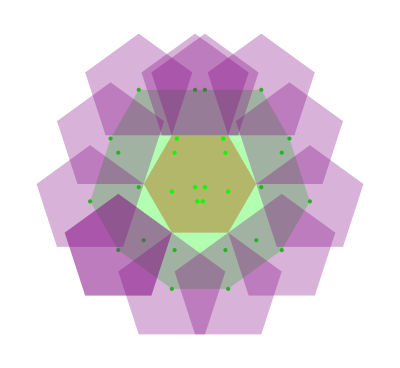

```mathematica
region1=Polygon[CirclePoints[6]];
robot=Polygon[CirclePoints[5]];
Graphics[{
Opacity[0.4],
Red,region1,
(*Blue,robot,*)
Opacity[1],Green,


(*find the coordinates of the convex hull:*)

pts =Flatten[Table[ Table[region1⟦1,i⟧-robot⟦1,j⟧,{i,1,Length[region1⟦1⟧]}],{j,1,Length[robot⟦1⟧]}],1];cvhullPt=#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts];
Point[pts],

Opacity[0.3],
Polygon[findConvexHullCoordsConvexPolysAS[region1,robot]],
(* draw the robot at the corners of the convex hull*)
Purple,
Table[Polygon[cvhullPt⟦i⟧+#&/@ robot⟦1⟧],{i,1,Length[cvhullPt]}]
}]
```